# Visualizing all Relationship

## 0101から0310までの30人の人間関係を可視化

## データ入力

### データのインポート

```mathematica
matrix = Import["~/Desktop/data/matrix.txt", "Data"]  /. 0->Infinity
```

```mathematica
Dimensions[matrix]
```

{30,30}

### ラベル付け

```mathematica
graphLabel={"0101","0102","0103","0104","0105","0106","0107","0108","0109", "0110", "0201","0202","0203","0204","0205","0206","0207","0208","0209","0220","0301","0302","0303","0304","0305","0306","0307","0308","0309","0330"};
```

### グラフの生成

```mathematica
f[pts_List,e_]:= Block[{s = 0.015,weight = PropertyValue[{labeledGraph,e},EdgeWeight]},
{
Arrowheads[Tiny], AbsoluteThickness[weight * 0.05], Arrow[pts]
}]
```

## コミュニティの可視化

### 多くの辺が同一コミュニティ内の頂点同士を繋いでおり，比較的少数の 辺が他のコミュニティの頂点と繋がっているコミュニティを求める

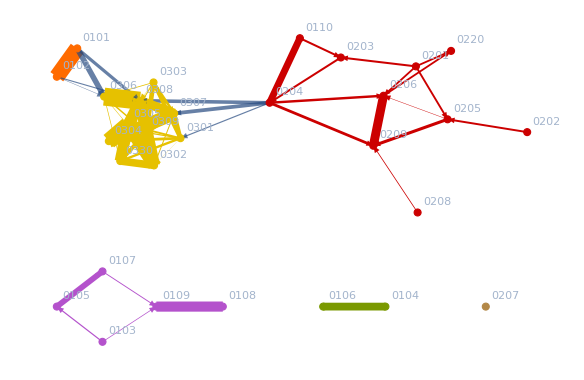

```mathematica
labeledGraph = Graph[WeightedAdjacencyGraph[matrix],VertexLabels-> Table[i -> graphLabel[[i]], {i,30}], EdgeShapeFunction->f]
Communities=FindGraphCommunities[labeledGraph];HighlightGraph[labeledGraph,Map[Subgraph[labeledGraph,#]&,Communities]]
```

### モジュールに基づくグラフ

```mathematica
CommunityGraphPlot[labeledGraph]
```

-Graphics-

### 階層に基づくグラフ

```mathematica
CommunityGraphPlot[labeledGraph, Method->"Hierarchical"]
```